u[0.4] is approximately: 1.46563

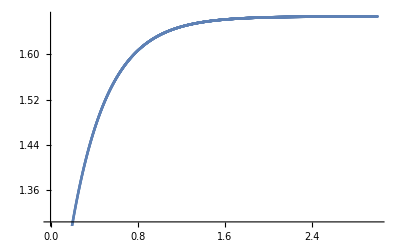

{{u→Function[{x},1/3 ⅇ^(-3 x) (-2+5 ⅇ^(3 x))]}}

u[0.4] is exactly: 1.46587

```mathematica
tMax = 3;
h = 0.001;
n = Ceiling[tMax/h];
y = Table[0,{n+1}];
y[[1]] = 1;

(* Holds the number of steps i so that i*h=0.4 *)
stepsToPoint = 0.4/h;

For[i = 1,i<n+1,i++,
y[[i+1]] = y[[i]] + h*(-3*y[[i]]+5)
];

Print["u[0.4] is approximately: ",y[[stepsToPoint]]];
ListPlot[Table[{i*h,y[[i]]},{i,0,n+1}]]
(* Find actual solution in order to compare to approximate solution *)
DSolve[{u'[x]== -3*u[x]+5,u[0]==1},u,x]
actual = (1/3*E^(-3*0.4))*(-2+5*E^(3*0.4));
Print["u[0.4] is exactly: ",actual];
```